# Transfer function for full LME

```mathematica
H := {{     ω,     0},
      {     0,         0}} ;
 J := {{     0,     γ },
      {     0,    0}} ;
ℐ[n_]:=IdentityMatrix[n];
```

```mathematica
L1 := KroneckerProduct[ℐ[2], H]- KroneckerProduct[Hᵀ,ℐ[2]];
L2 := (KroneckerProduct[2*J*, J] - KroneckerProduct[ℐ[2],J†.J]- KroneckerProduct[Jᵀ.J*, ℐ[2]])/2;
L :=Assuming[_∈Reals, Simplify[ - ⅈ*L1+L2 ]];
MatrixForm[Expand[L]]
```

(0 | 0 | 0 | γ^2
0 | -γ^2/2+ⅈ ω | 0 | 0
0 | 0 | -γ^2/2-ⅈ ω | 0
0 | 0 | 0 | -γ^2)

```mathematica
Subscript[M, bρ] := {{0, 0, 1, 1},
          {1,-ⅈ,0,0},
          {1,  ⅈ,0,0},
          {0,0,-1,1} }/2 ;
Subscript[ρ, 0] :={{1, 0}, {0, 0}};
Subscript[ρ, 1] :={{0, 0}, { 0, 1}};
Subscript[ρ, x] :={{1, 1}, {1, 1}}/2;
Subscript[ρ, y]:={{1, -ⅈ}, {ⅈ, 1}}/2;
Subscript[M, ρb] := {{0, 1, 1, 0},
      {0,ⅈ,-ⅈ,0},
      {1,  0,0,-1},
      {1,0,0,1} } 
Subscript[b, 0] :={0, 0, 1, 1}ᵀ;
Subscript[b, 1] :={0, 0, -1, 1}ᵀ;
Subscript[b, x] :={1, 0, 0, 1}ᵀ;
Subscript[b, y]:={0, 1, 0, 1}ᵀ;
Equal[Subscript[M, bρ].Subscript[M, ρb] ,ℐ[4]]
Subscript[A, symb] :=Simplify[Subscript[M, ρb].L.Subscript[M, bρ]]
```

True

```mathematica
TransferFunction[A_, b_]:= Assuming[{γ∈Reals,ω∈Reals},Simplify[Inverse[s*ℐ[4]- A].b]];
```

```mathematica
Subscript[Gx, symb] :=Simplify[TransferFunction[Subscript[A, symb], Subscript[b, x] ]];
```

```mathematica
Subscript[Ac, SID] = ({{0, 25, 0, 0}, {-25, -4π/2, 0, 0}, {0, 0, -4π/2, 4π/2}, {0, 0, 0, 0}})

Subscript[b, x] :={1, 0, 0, 1}ᵀ;
Subscript[Gx, SID]=TransferFunction[Subscript[Ac, SID], Subscript[b, x] ]
```

{{0,25,0,0},{-25,-2 π,0,0},{0,0,-2 π,2 π},{0,0,0,0}}

{(2 π+s)/(625+2 π s+s^2),-25/(625+2 π s+s^2),(2 π)/(2 π s+s^2),1/s}

```mathematica
CoefficientList[Expand[Numerator[Assuming[_∈Reals, Simplify[Expand[Together[Subscript[Gx, SID] - Subscript[Gx, symb]]]]]]],s]
```

{{-1250 γ^2+2 π γ^4+8 π ω^2,-2500+4 π γ^2+γ^4+4 ω^2,2 γ^2},{-25 γ^4+2500 ω-100 ω^2,-100 γ^2+8 π ω,-100+4 ω},{2 π-γ^2},{}}

```mathematica
$Assumptions=_∈Reals
obj =Simplify[Total[Re[(Flatten[CoefficientList[Numerator[Together[Subscript[Gx, SID] - Subscript[Gx, symb]]],s]])^2]]];
Variables[obj]
```

_∈ℝ

{γ,ω}

```mathematica
obj
```

4 γ^4+(-2 π+γ^2)^2+16 (-25+ω)^2+(100 γ^2-8 π ω)^2+625 (γ^4+4 (-25+ω) ω)^2+4 (-625 γ^2+π γ^4+4 π ω^2)^2+(4 π γ^2+γ^4+4 (-625+ω^2))^2

```mathematica
Expand[obj]
```

6260000+4 π^2-20004 π γ^2+1567505 γ^4+16 π^2 γ^4-4992 π γ^6+626 γ^8+4 π^2 γ^8-800 ω-1600 π γ^2 ω-125000 γ^4 ω+6230016 ω^2+64 π^2 ω^2-19968 π γ^2 ω^2+5008 γ^4 ω^2+32 π^2 γ^4 ω^2-500000 ω^3+10016 ω^4+64 π^2 ω^4

```mathematica
$Assumptions=_∈Reals
sol= NMinimize[obj,{ω,γ}]
```

_∈ℝ

{347633.,{ω→23.5171,γ→3.43252}}

```mathematica
{6.526025012796372*^6,{ω->-0.00006668519446357043,γ->-1.5552963522834533*^-8}}
```

{6.52603×10^6,{ω→-0.0000666852,γ→-1.5553×10^-8}}

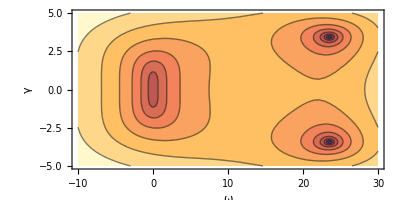

```mathematica
Show[ContourPlot[Log[obj], {ω,-10,30},{γ,-5,5}, Axes->True,AxesLabel ->{ω,γ} ,LabelStyle-> Bold,AspectRatio->1/2,PlotRange->All],PerformanceGoal->"Quality"]
```

```mathematica
3
```

3